# Comparison of SQ- 3 / 8 Helix OD, CD Spektren

```mathematica
<<ModList.m
<<StylePlot.m
```

## Experiment

```mathematica
SetDirectory["/home/lindorfer/Post-Doc/TRCD/Experiment"];
Data=Import["Abs und CD pSQ-R2s in acetone.txt","Table"];
Data=Drop[Data,3];

ExpCD=Take2[Data,1,2];
ExpOD=Take2[Data,1,3];
```

## Linear CD & OD Spectra

```mathematica
SetDirectory[NotebookDirectory[]]

OD=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ8_eps2/CD_OD_Dis.out","Table"];
OD=Take2[OD,1,3];

CD=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ8_eps2/CD_OD_Dis.out","Table"];
CD=Take2[CD,1,2];

ODSQ3=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ3/CD_OD_Dis.out","Table"];
ODSQ3=Take2[ODSQ3,1,3];

CDSQ3=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ3/CD_OD_Dis.out","Table"];
CDSQ3=Take2[CDSQ3,1,2];

ODSQ16=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ16/CD_OD_Dis.out","Table"];
ODSQ16=Take2[ODSQ16,1,3];

CDSQ16=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ16/CD_OD_Dis.out","Table"];
CDSQ16=Take2[CDSQ16,1,2];

ODSQ24=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ24/CD_OD_Dis.out","Table"];
ODSQ24=Take2[ODSQ24,1,3];

CDSQ24=Import["/home/lindorfer/Post-Doc/TRCD/Spectra/Results/SQ24/CD_OD_Dis.out","Table"];
CDSQ24=Take2[CDSQ24,1,2];
```

/home/lindorfer/Post-Doc/TRCD/Spectra

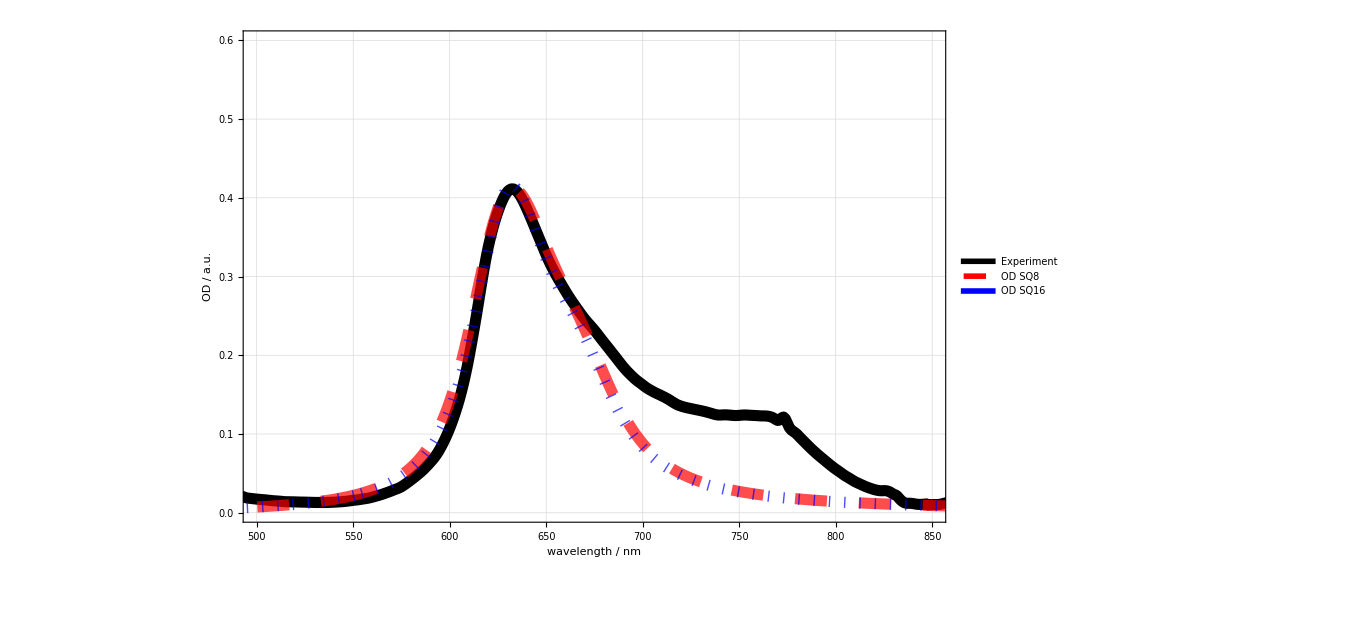

```mathematica
PlotLinSpecOD=StyleListPlot[{ExpOD,ShiftX[ScaleY[OD,3],-6],ShiftX[ScaleY[ODSQ16,6.2],-5]},

PlotStyle->{{Black,Thickness[0.008]},{Red,Opacity[0.7],Dashing[0.023],Thickness[0.008]},{Blue,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Green,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Yellow,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]}},
PlotRange->{{500,850},{0,0.6}},
FrameLabels->{{"OD / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"Experiment","OD SQ8","OD SQ16"}],
LegendPlacement->{{0.15,0.75}},
PlotLegendsLineColor->{Directive[Black,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashing[0.028]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5],Dashing[0.028]]},
GridLinesStyle->Directive[Gray, Dashed],
LegendSpacing->{0.1,-1.2},
ImageSize->1000
]
```

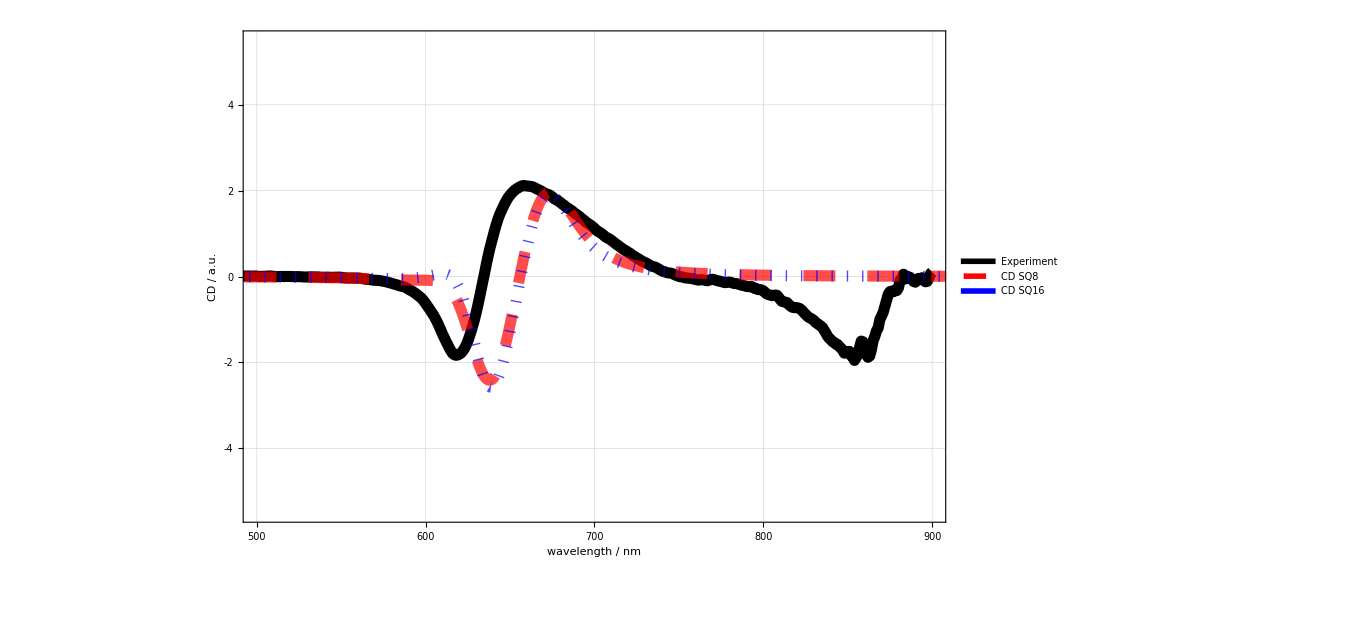

```mathematica
PlotLinSpecCD=StyleListPlot[{ExpCD,ShiftX[ScaleY[CD,0.8],-6],ShiftX[ScaleY[CDSQ16,2],-5]},

PlotStyle->{{Black,Thickness[0.008]},{Red,Opacity[0.7],Dashing[0.023],Thickness[0.008]},{Blue,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Green,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]}},
PlotRange->{{500,900},{-5.5,5.5}},
FrameLabels->{{"CD / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"Experiment","CD SQ8","CD SQ16"}],
LegendPlacement->{{0.15,0.25}},
PlotLegendsLineColor->{Directive[Black,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashing[0.028]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5],Dashing[0.028]]},
GridLinesStyle->Directive[Gray, Dashed],
LegendSpacing->{0.1,-1.2},
ImageSize->1000
]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
Export["OD_SQ816.pdf",PlotLinSpecOD]
Export["CD_SQ816.pdf",PlotLinSpecCD]
```

/home/lindorfer/Post-Doc/TRCD/Spectra

OD_SQ816.pdf

CD_SQ816.pdf